```mathematica
(*Дифференциальное уравнение:du/dt-du/dx=phi(x,t)*)
(*Шаблон:{(x_m,t_n),(x_{m+1},t_n),(x_m,t_{n+1})}*)
ClearAll["Global`*"];

(*Параметры сетки*)
h=Symbol["h"]; (*шаг по пространству*)
τ=Symbol["τ"]; (*шаг по времени*)

(*Представление решения в виде u_m^n=λ^n Exp[I m α]*)
(*Разностная схема для шаблона {(x_m,t_n),(x_{m+1},t_n),(x_m,t_{n+1})}*)
(*Аппроксимируем производные:du/dt~(u_m^{n+1}-u_m^n)/τ du/dx~(u_{m+1}^n-u_m^n)/h*)

(*Разностное уравнение*)
diffEq=(u[m,n+1]-u[m,n])/τ-(u[m+1,n]-u[m,n])/h;

(*Подставляем представление решения u_m^n=λ^n Exp[I m α]*)
diffEqSubstituted=diffEq/. {u[m,n+1]->λ^(n+1) Exp[I m α],u[m,n]->λ^n Exp[I m α],u[m+1,n]->λ^n Exp[I (m+1) α]};

(*Упрощаем уравнение*)
simplifiedEq=Simplify[diffEqSubstituted/(λ^n Exp[I m α])];

Print["Упрощенное уравнение: ",simplifiedEq," = 0"];
```

Упрощенное уравнение: (h (-1+λ)+τ-ⅇ^(ⅈ α) τ)/(h τ) = 0

```mathematica
(*Выражаем λ*)
lambdaSolution=Solve[simplifiedEq==0,λ];
λValue=λ/. First[lambdaSolution];

(*Упрощаем выражение для λ*)
λValue=Simplify[λValue];

(*Обозначаем r=τ/h*)
r=τ/h;
λValue=λValue/. {τ->r h};

(*Упрощаем окончательно*)
λValue=Simplify[λValue];

Print["Характеристическое уравнение:"];
Print["λ = ",λValue];
```

Характеристическое уравнение:

λ = 1+((-1+ⅇ^(ⅈ α)) τ)/h

```mathematica
(*Анализ устойчивости*)
(*Необходимое условие устойчивости Неймана: |λ| <=1*)

Print["\nАнализ устойчивости:"];

(*Модуль λ*)
absLambda=ComplexExpand[Abs[λValue]];
Print["|λ| = ",absLambda];
```

Анализ устойчивости:

|λ| = √((1+(τ (-1+Cos[α]))/h)^2+(τ^2 Sin[α]^2)/h^2)

```mathematica
(*Условие устойчивости: |λ| <=1*)
Print["Условие устойчивости: |λ| <= 1"];

(*Для нашего случая a=1 (из уравнения du/dt-du/dx)*)
(*В общем виде:du/dt-a du/dx,у нас a=1*)
a=1;

(*Исследуем зависимость от r=τ/h*)
Print["\nИсследование зависимости от r = τ/h:"];
```

Условие устойчивости: |λ| <= 1

Исследование зависимости от r = τ/h:

```mathematica
(*Модуль λ как функция r и α*)
absLambdaFunc[rVal_,αVal_]:=Abs[1-rVal+rVal Exp[I αVal]];

(*Анализ для различных r*)
Print["r = 0.5:"];
maxVal05=NMaxValue[{absLambdaFunc[0.5,α],0<=α<=2 Pi},α];
Print["Максимальное |λ| при r=0.5: ",maxVal05];
Print["Условие устойчивости выполняется: ",maxVal05<=1];

Print["r = 1:"];
maxVal1=NMaxValue[{absLambdaFunc[1,α],0<=α<=2 Pi},α];
```

r = 0.5:

Максимальное |λ| при r=0.5: 1.

Условие устойчивости выполняется: True

r = 1:

```mathematica
Print["Максимальное |λ| при r=1: ",maxVal1];
Print["Условие устойчивости выполняется: ",maxVal1<=1];

Print["r = 1.5:"];
maxVal15=NMaxValue[{absLambdaFunc[1.5,α],0<=α<=2 Pi},α];
Print["Максимальное |λ| при r=1.5: ",maxVal15];
Print["Условие устойчивости выполняется: ",maxVal15<=1];
```

Максимальное |λ| при r=1: -1.

Условие устойчивости выполняется: True

r = 1.5:

Максимальное |λ| при r=1.5: 2.

Условие устойчивости выполняется: False

Графики зависимости |λ| от α для различных r:

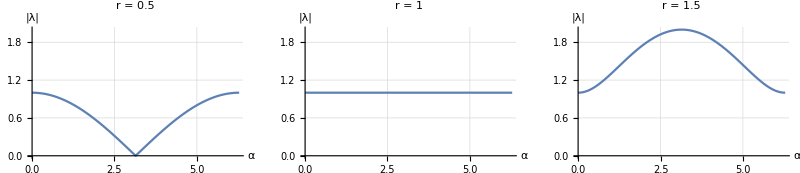

=== РЕЗУЛЬТАТЫ ИССЛЕДОВАНИЯ ===

1. Характеристическое число: λ = 1 - r + r Exp[Iα], где r = τ/h

2. Модуль характеристического числа: |λ| = |1 - r + r Exp[Iα]|

3. Условие устойчивости: |λ| <= 1 для всех α

4. Анализ:

- При r <= 1: |λ| <= 1 для всех α

- При r > 1: существуют α, для которых |λ| > 1

5. ВЫВОД: Разностная схема устойчива при r = τ/h <= 1

6. Сходимость: При r <= 1 схема сходится с порядком O(τ + h)

```mathematica
(*Визуализация для конкретных значений r*)
Print["\nГрафики зависимости |λ| от α для различных r:"];

plot05=Plot[absLambdaFunc[0.5,α],{α,0,2 Pi},PlotRange->{0,2},AxesLabel->{"α","|λ|"},PlotLabel->"r = 0.5",GridLines->Automatic];

plot1=Plot[absLambdaFunc[1,α],{α,0,2 Pi},PlotRange->{0,2},AxesLabel->{"α","|λ|"},PlotLabel->"r = 1",GridLines->Automatic];

plot15=Plot[absLambdaFunc[1.5,α],{α,0,2 Pi},PlotRange->{0,2},AxesLabel->{"α","|λ|"},PlotLabel->"r = 1.5",GridLines->Automatic];

GraphicsRow[{plot05,plot1,plot15},ImageSize->800]

(*Вывод результатов*)
Print["\n=== РЕЗУЛЬТАТЫ ИССЛЕДОВАНИЯ ==="];
Print["1. Характеристическое число: λ = 1 - r + r Exp[Iα], где r = τ/h"];
Print["2. Модуль характеристического числа: |λ| = |1 - r + r Exp[Iα]|"];
Print["3. Условие устойчивости: |λ| <= 1 для всех α"];
Print["4. Анализ:"];
Print["   - При r <= 1: |λ| <= 1 для всех α"];
Print["   - При r > 1: существуют α, для которых |λ| > 1"];
Print["5. ВЫВОД: Разностная схема устойчива при r = τ/h <= 1"];
Print["6. Сходимость: При r <= 1 схема сходится с порядком O(τ + h)"];
```